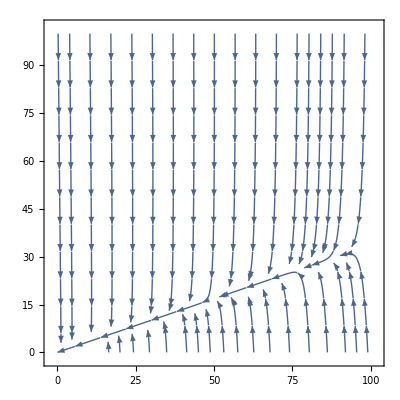

```mathematica
StreamPlot[{-5x+3y,100x-301y},{x,0,100},{y,0,100}]
```

```mathematica
result = NDSolve[{x'[t]==-5x[t]+3y[t],y'[t]==100x[t]-301y[t],x[0]==52.29,y[0]==83.82},{x,y},{t,0,20}]
```

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
result
```

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
xValues = result[[1,1]]
```

x→InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
yValues = result[[1,2]]
```

y→InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
Plot[{xValues[t],yValues[t]},{t,0,1}]
```

-Graphics-